```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
```

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->14}];
SetOptions[Graphics,BaseStyle->{FontSize->14}];
SetOptions[ParametricPlot,BaseStyle->{FontSize->14}];
SetOptions[LogPlot,BaseStyle->{FontSize->14}];
```

```mathematica
mas=4.84814*^-9;
AU=1.495978707*^11;
c=2.99792458*^8;
pc=3.0857*^16;
re=2.8179403227*^-15;
```

```mathematica
dlens=389.*pc;
dpsr=620.*pc;
λ=c/314.5*^6;
```

```mathematica
λA=1.*^5*AU;
T=0.01*AU;
A=0.3*AU;
inc=1.*^-5;
```

```mathematica
R=λA^2/(4π^2A Cos[inc]^3 Sqrt[1.-λA^2./(4.π^2 A^2)Tan[inc]^2]);
s=1.-dlens/dpsr;
r=R/dlens;
t=T/dlens; 
R/pc
T/AU
r
t/mas
```

4829.05

0.01

12.414

0.0257067

```mathematica
Δn:=-λ^2/(2π)Δne re
```

```mathematica
β:=θ-s Δn t Sqrt[r/2]/θ^{3/2}
```

```mathematica
μ:=1./D[β,θ]
```

```mathematica
Δnes={0.003,0.03,0.3,3.}*1.*^6;
```

```mathematica
tsc=Solve[{beta==β,Δne<0,θ≥0},θ,Reals];
tsd=Solve[{beta==β,Δne>0,θ≥0},θ,Reals];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

## Plots of the Lens Behaviour

Less::nord: Invalid comparison with 0.  + 1.1543×10^7\ ⅈ
 attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

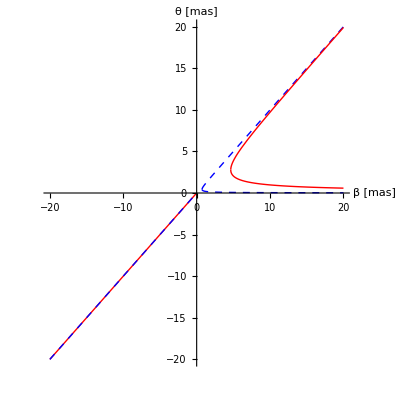

```mathematica
ShowLegend[Show[
ParametricPlot[{
{beta/mas,θ/mas/.tsd[[1]]/.Δne->Δnes[[1]]},
{beta/mas,θ/mas/.tsd[[1]]/.Δne->Δnes[[3]]},
{beta/mas,θ/mas/.tsd[[2]]/.Δne->Δnes[[1]]},
{beta/mas,θ/mas/.tsd[[2]]/.Δne->Δnes[[3]]}
},{beta,-20*mas,20*mas},PlotStyle->{Directive[Blue,Dashed],Directive[Red]}],
ParametricPlot[{
{beta/mas,beta/mas},
{beta/mas,beta/mas}
},{beta,-20*mas,-t/2},PlotStyle->{Directive[Red],Directive[Blue,Dashed]}]
,PlotRange->{{-20,20},{-20,20}},AxesLabel->{"β [mas]","θ [mas]"},ImageSize->400,ImagePadding->{{0,60},{0,60}},AspectRatio->1],{{{Graphics[{Directive[Blue,Dashed],Line[{{0,0},{3,0}}]}],ToString[Δnes[[1]]/1.*^6]},{Graphics[{Red,Line[{{0,0},{3,0}}]}],ToString[Δnes[[3]]/1.*^6]}},LegendPosition->{0.,-0.7},LegendSize->{0.5,0.4},LegendShadow->False,LegendLabel->"Δn_e [cm^-3]"},LegendLabelSpace->1,LegendSpacing->0.5]
```

Less::nord: Invalid comparison with 0.  - 1.1543×10^7\ ⅈ
 attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

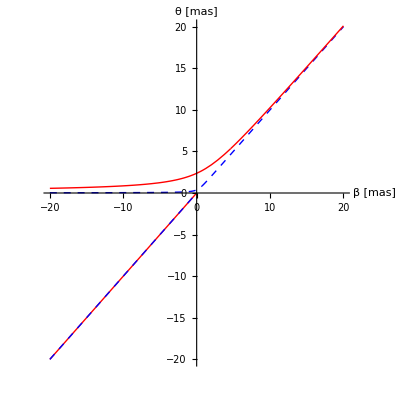

```mathematica
ShowLegend[Show[
ParametricPlot[{
{beta/mas,θ/mas/.tsc[[1]]/.Δne->-Δnes[[1]]},
{beta/mas,θ/mas/.tsc[[1]]/.Δne->-Δnes[[3]]},
{beta/mas,θ/mas/.tsc[[2]]/.Δne->-Δnes[[1]]},
{beta/mas,θ/mas/.tsc[[2]]/.Δne->-Δnes[[3]]}
},{beta,-20*mas,20*mas},PlotStyle->{Directive[Blue,Dashed],Directive[Red]}],
ParametricPlot[{
{beta/mas,beta/mas},
{beta/mas,beta/mas}
},{beta,-20*mas,-t/2},PlotStyle->{Directive[Red],Directive[Blue,Dashed]}]
,PlotRange->{{-20,20},{-20,20}},AxesLabel->{"β [mas]","θ [mas]"},ImageSize->400,ImagePadding->{{0,60},{0,60}},AspectRatio->1],{{{Graphics[{Directive[Blue,Dashed],Line[{{0,0},{3,0}}]}],ToString[-Δnes[[1]]/1.*^6]},{Graphics[{Red,Line[{{0,0},{3,0}}]}],ToString[-Δnes[[3]]/1.*^6]}},LegendPosition->{0.,-0.7},LegendSize->{0.5,0.4},LegendShadow->False,LegendLabel->"Δn_e [cm^-3]"},LegendLabelSpace->1,LegendSpacing->0.5]
```

Less::nord: Invalid comparison with 0.  + 1.1543×10^7\ ⅈ
 attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

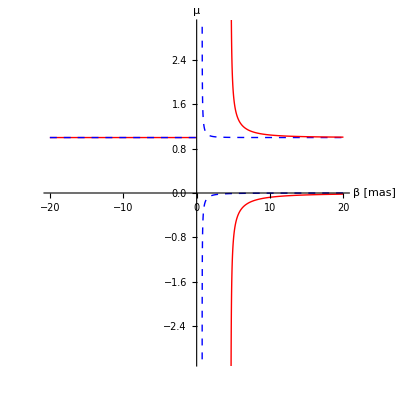

```mathematica
ShowLegend[Show[
ParametricPlot[{
{beta/mas,μ/.tsd[[1]]/.Δne->Δnes[[1]]},
{beta/mas,μ/.tsd[[1]]/.Δne->Δnes[[3]]},
{beta/mas,μ/.tsd[[2]]/.Δne->Δnes[[1]]},
{beta/mas,μ/.tsd[[2]]/.Δne->Δnes[[3]]}
},{beta,-20*mas,20*mas},PlotStyle->{Directive[Blue,Dashed],Directive[Red]}],
ParametricPlot[{
{beta/mas,1.},
{beta/mas,1.}
},{beta,-20*mas,-t/2},PlotStyle->{Directive[Red],Directive[Blue,Dashed]}]
,PlotRange->{{-20,20},{-3,3}},AxesLabel->{"β [mas]","μ"},ImageSize->400,ImagePadding->{{0,60},{0,60}},AspectRatio->1],{{{Graphics[{Directive[Blue,Dashed],Line[{{0,0},{3,0}}]}],ToString[Δnes[[1]]/1.*^6]},{Graphics[{Red,Line[{{0,0},{3,0}}]}],ToString[Δnes[[3]]/1.*^6]}},LegendPosition->{-0.85,-0.7},LegendSize->{0.5,0.4},LegendShadow->False,LegendLabel->"Δn_e [cm^-3]"},LegendLabelSpace->1,LegendSpacing->0.5]
```

Less::nord: Invalid comparison with 0.  - 1.1543×10^7\ ⅈ
 attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

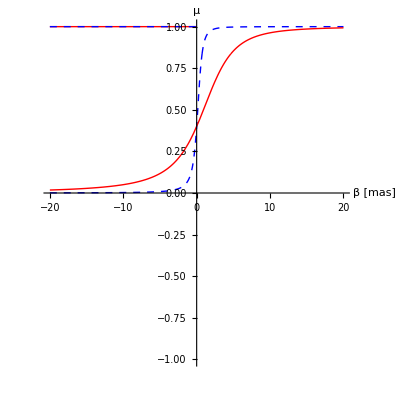

```mathematica
ShowLegend[Show[
ParametricPlot[{
{beta/mas,μ/.tsc[[1]]/.Δne->-Δnes[[1]]},
{beta/mas,μ/.tsc[[1]]/.Δne->-Δnes[[3]]},
{beta/mas,μ/.tsc[[2]]/.Δne->-Δnes[[1]]},
{beta/mas,μ/.tsc[[2]]/.Δne->-Δnes[[3]]}
},{beta,-20*mas,20*mas},PlotStyle->{Directive[Blue,Dashed],Directive[Red]}],
ParametricPlot[{
{beta/mas,1.},
{beta/mas,1.}
},{beta,-20*mas,-t/2},PlotStyle->{Directive[Red],Directive[Blue,Dashed]}]
,PlotRange->{{-20,20},{-1,1}},AxesLabel->{"β [mas]","μ"},ImageSize->400,ImagePadding->{{0,60},{0,60}},AspectRatio->1],{{{Graphics[{Directive[Blue,Dashed],Line[{{0,0},{3,0}}]}],ToString[-Δnes[[1]]/1.*^6]},{Graphics[{Red,Line[{{0,0},{3,0}}]}],ToString[-Δnes[[3]]/1.*^6]}},LegendPosition->{0.,-0.7},LegendSize->{0.5,0.4},LegendShadow->False,LegendLabel->"Δn_e [cm^-3]"},LegendLabelSpace->1,LegendSpacing->0.5]
```

```mathematica
ticks={{Log[10,0.00000001],"10^-8"},{Log[10,0.00000002],},{Log[10,0.00000003],},{Log[10,0.00000004],},{Log[10,0.00000005],},{Log[10,0.00000006],},{Log[10,0.00000007],},{Log[10,0.00000008],},{Log[10,0.00000009],},{Log[10,0.0000001],"10^-7"},{Log[10,0.0000002],},{Log[10,0.0000003],},{Log[10,0.0000004],},{Log[10,0.0000005],},{Log[10,0.0000006],},{Log[10,0.0000007],},{Log[10,0.0000008],},{Log[10,0.0000009],},{Log[10,0.000001],"10^-6"},{Log[10,0.000002],},{Log[10,0.000003],},{Log[10,0.000004],},{Log[10,0.000005],},{Log[10,0.000006],},{Log[10,0.000007],},{Log[10,0.000008],},{Log[10,0.000009],},{Log[10,0.00001],"10^-5"},{Log[10,0.00002],},{Log[10,0.00003],},{Log[10,0.00004],},{Log[10,0.00005],},{Log[10,0.00006],},{Log[10,0.00007],},{Log[10,0.00008],},{Log[10,0.00009],},{Log[10,0.0001],"10^-4"},{Log[10,0.0002],},{Log[10,0.0003],},{Log[10,0.0004],},{Log[10,0.0005],},{Log[10,0.0006],},{Log[10,0.0007],},{Log[10,0.0008],},{Log[10,0.0009],},{Log[10,0.001],"10^-3"},{Log[10,0.002],},{Log[10,0.003],},{Log[10,0.004],},{Log[10,0.005],},{Log[10,0.006],},{Log[10,0.007],},{Log[10,0.008],},{Log[10,0.009],},{Log[10,0.01],0.01},{Log[10,0.02],},{Log[10,0.03],},{Log[10,0.04],},{Log[10,0.05],},{Log[10,0.06],},{Log[10,0.07],},{Log[10,0.08],},{Log[10,0.09],},{Log[10,10^-1],0.1},{Log[10,0.2],},{Log[10,0.3],},{Log[10,0.4],},{Log[10,0.5],},{Log[10,0.6],},{Log[10,0.7],},{Log[10,0.8],},{Log[10,0.9],},{Log[10,1],1},{Log[10,2],},{Log[10,3],},{Log[10,4],},{Log[10,5],},{Log[10,6],},{Log[10,7],},{Log[10,8],},{Log[10,9],},{Log[10,10],10},{Log[10,20],},{Log[10,30],},{Log[10,40],},{Log[10,50],},{Log[10,60],},{Log[10,70],},{Log[10,80],},{Log[10,90],},{Log[10,100],100},{Log[10,200],},{Log[10,300],},{Log[10,400],},{Log[10,500],},{Log[10,600],},{Log[10,700],},{Log[10,800],},{Log[10,900],},{Log[10,1000],1000}};
```

```mathematica
Δθref:=(s*Abs[Δn]*t*Sqrt[r/2])^(2./5.)
```

0.0257067

Less::nord: Invalid comparison with 0.  - 0.0837905\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.  + 0.0837905\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.  - 0.0837905\ ⅈ
 attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

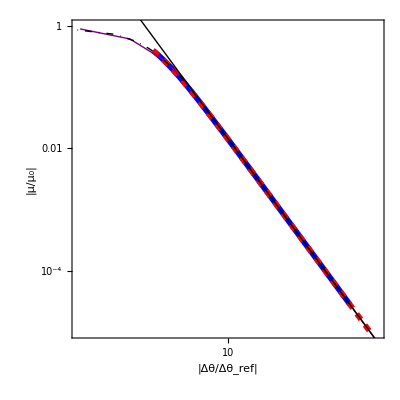

```mathematica
ShowLegend[Show[ParametricPlot[{
{Log[10,Abs[(((θ/.tsc[[1]])-beta)/Δθref)]/.beta->-b/.Δne->-Δnes[[3]]],
Log[10,Abs[μ/.tsc[[1]]]/.Δne->-Δnes[[3]]/.beta->-b]},
{Log[10,Abs[(((θ/.tsc[[1]])-beta)/Δθref)]/.beta->-b/.Δne->-Δnes[[1]]],
Log[10,Abs[μ/.tsc[[1]]]/.Δne->-Δnes[[1]]/.beta->-b]},
{Log[10,Abs[(((θ/.tsd[[1]])-(θ/.tsd[[2]]))/Δθref)]/.beta->b/.Δne->Δnes[[1]]],
Log[10,Abs[(μ/.tsd[[1]])/(μ/.tsd[[2]])]/.beta->b/.Δne->Δnes[[1]]]},
{Log[10,Abs[(((θ/.tsd[[1]])-(θ/.tsd[[2]]))/Δθref)]/.beta->b/.Δne->Δnes[[3]]],
Log[10,Abs[(μ/.tsd[[1]])/(μ/.tsd[[2]])]/.beta->b/.Δne->Δnes[[3]]]}
},
{b,0.001*mas,1000.*mas},PlotPoints->100,Frame->{True,True,False,False},Axes->False,
FrameTicks->{ticks,ticks,ticks,ticks},PlotRange->{{-1.,3.},{-5.,0.}},FrameLabel->{"|Δθ/Δθ_ref|","|μ/μ_0|"},PlotStyle->{Directive[Blue,Thickness[0.01]],Directive[Red,Dashed,Thickness[0.01]],Directive[Purple],Directive[Black,DotDashed, Thick]},ImageSize->400,ImagePadding->{{60,60},{60,60}},AspectRatio->1],
Plot[Log[10,(2/3)]-5/3*x,{x,-1,3},PlotStyle->Black]
],{{{Graphics[{Directive[Blue,Thick],Line[{{0,0},{2,0}}]}],"- "<>ToString[Δnes[[3]]/1.*^6]},{Graphics[{Directive[Red, Dashed,Thick],Line[{{0,0},{2,0}}]}],"- "<>ToString[Δnes[[1]]/1.*^6]},{Graphics[{Directive[Purple],Line[{{0,0},{2,0}}]}],ToString[Δnes[[1]]/1.*^6]},{Graphics[{Directive[Black,DotDashed,Thick],Line[{{0,0},{2,0}}]}],ToString[Δnes[[3]]/1.*^6]}},LegendPosition->{0.15,0.0},LegendSize->{0.5,0.6},LegendShadow->False,LegendLabel->"Δn_e [cm^-3]"}]
```

```mathematica
βinner = θ+s Δn Sqrt[2 r/(θ+t/2)]
```

θ-7.5656×10^-16 Δne √(1/(6.23149×10^-11+θ))

```mathematica
muinner=1./(1.-s*Δn*Sqrt[r/2]/(θ+t/2)^(3/2))
```

1./(1.+(3.7828×10^-16 Δne)/((6.23149×10^-11+θ)^(3/2)))

```mathematica
tinner=Solve[{betainner==βinner},θ,Reals];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
tinner
```

{{θ→ConditionalExpression[Root[-1. Δne^2+4.49914×10^50 betainner^2 #1^3-8.99827×10^50 betainner #1^4+4.49914×10^50 #1^5&,1],(0<Δne<3.94322×10^24 √(betainner^5)&&betainner>0)||(betainner<0&&Δne<0)||(Δne<-3.94322×10^24 √(betainner^5)&&betainner>0)]},{θ→ConditionalExpression[Root[-1. Δne^2+4.49914×10^50 betainner^2 #1^3-8.99827×10^50 betainner #1^4+4.49914×10^50 #1^5&,2],0<Δne<3.94322×10^24 √(betainner^5)&&betainner>0]},{θ→ConditionalExpression[Root[-1. Δne^2+4.49914×10^50 betainner^2 #1^3-8.99827×10^50 betainner #1^4+4.49914×10^50 #1^5&,3],-3.94322×10^24 √(betainner^5)<Δne<0&&betainner>0]}}

```mathematica
bmin=t/2+s*Δn*Sqrt[2r/t];
bminc1 = (Δne/-3.94322*^24)^(2/5);
bmaxc2 = (Δne/-3.94322*^24)^(2/5);
```

```mathematica
{bmin/mas,  bminc1/mas,  bmaxc2/mas}/.Δne->-Δnes[[1]]
```

{41.948,0.736093,0.736093}

```mathematica
t/2+s*Δn*Sqrt[2*r/t]
```

6.23149×10^-11-6.77692×10^-11 Δne

```mathematica
(t/2+s Δn Sqrt[2*r/t]/.Δne->-Δnes[[1]])/mas
```

41.948

```mathematica
(((θ/.tinner[[3]])-betainner))/.Δne->-Δnes[[1]]/.betainner->100.*mas
```

4.18977×10^-13

```mathematica
(muinner/.tinner[[3]])/.Δne->-Δnes[[1]]/.betainner->100.*mas
```

1.00337

```mathematica
ParametricPlot[{
β
```

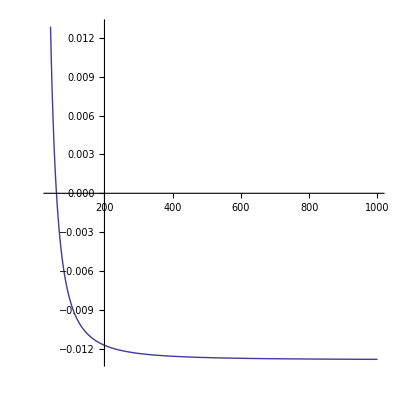

```mathematica
ParametricPlot[
{{betainner/mas/.Δne->-Δnes[[1]],θ/mas/.tinner[[1]]/.Δne->-Δnes[[1]]}},
{betainner,(t/2+s Δn Sqrt[2*r/t])/.Δne->-Δnes[[1]],1000.*mas},PlotRange->All,AspectRatio->1]
```

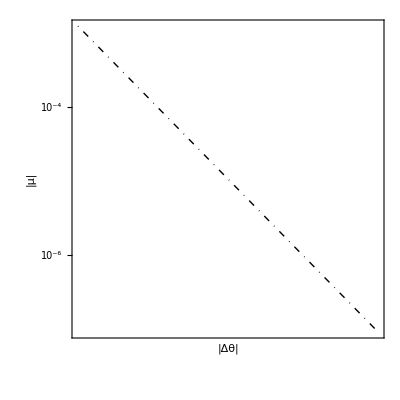

```mathematica
Show[ParametricPlot[{
{Log[10,Abs[(((θ/.tinner[[1]])-betainner))]/.Δne->-Δnes[[1]]],
Log[10,Abs[(muinner/.tinner[[1]])]/.Δne->-Δnes[[1]]]}},
{betainner,(t/2+s Δn Sqrt[2*r/t])/.Δne->-Δnes[[1]],1000.*mas},PlotPoints->100,Frame->{True,True,False,False},Axes->False,
FrameTicks->{ticks,ticks,ticks,ticks},PlotRange->All,FrameLabel->{"|Δθ|","|μ|"},PlotStyle->{Directive[Blue,Thickness[0.01]],Directive[Red,Dashed,Thickness[0.01]],Directive[Purple],Directive[Black,DotDashed, Thick]},ImageSize->400,ImagePadding->{{60,60},{60,60}},AspectRatio->1]
]
```

Less::nord: Invalid comparison with 0.  - 0.0837905\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.  + 0.0837905\ ⅈ
 attempted.

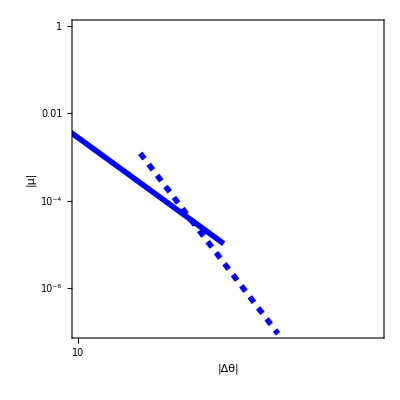

```mathematica
(*ShowLegend[*)
Show[ParametricPlot[{
{Log[10,Abs[(((θ/.tsc[[1]])-beta))/mas]/.beta->-b/.Δne->-Δnes[[1]]],
Log[10,Abs[μ/.tsc[[1]]]/.Δne->-Δnes[[1]]/.beta->-b]}},
{b,0.001*mas,1000.*mas},PlotPoints->100,Frame->{True,True,False,False},Axes->False,
FrameTicks->{ticks,ticks,ticks,ticks},PlotRange->{{1.,4.},{-7.,0.}},FrameLabel->{"|Δθ|","|μ|"},PlotStyle->{Directive[Blue,Thickness[0.01]]},ImageSize->400,ImagePadding->{{60,60},{60,60}},AspectRatio->1],ParametricPlot[{
{Log[10,Abs[(((θ/.tinner[[1]])-betainner))/mas]/.Δne->-Δnes[[1]]],
Log[10,Abs[(muinner/.tinner[[1]])]/.Δne->-Δnes[[1]]]}},
{betainner,(t/2+s Δn Sqrt[2*r/t])/.Δne->-Δnes[[1]],1000.*mas},PlotPoints->100,Frame->{True,True,False,False},Axes->False,
FrameTicks->{ticks,ticks,ticks,ticks},PlotRange->All,FrameLabel->{"|Δθ|","|μ|"},PlotStyle->{Directive[Blue,Dashed,Thickness[0.01]]},ImageSize->400,ImagePadding->{{60,60},{60,60}},AspectRatio->1]
]
(*,{{{Graphics[{Directive[Blue,Thick],Line[{{0,0},{2,0}}]}],"- "<>ToString[Δnes[[3]]/1.*^6]},{Graphics[{Directive[Red, Dashed,Thick],Line[{{0,0},{2,0}}]}],"- "<>ToString[Δnes[[1]]/1.*^6]},{Graphics[{Directive[Purple],Line[{{0,0},{2,0}}]}],ToString[Δnes[[1]]/1.*^6]},{Graphics[{Directive[Black,DotDashed,Thick],Line[{{0,0},{2,0}}]}],ToString[Δnes[[3]]/1.*^6]}},LegendPosition->{0.15,0.0},LegendSize->{0.5,0.6},LegendShadow->False,LegendLabel->"Δn_e [cm^-3]"}]*)
```

Less::nord: Invalid comparison with 0.  - 6.61778×10^8\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.  + 6.61778×10^8\ ⅈ
 attempted.

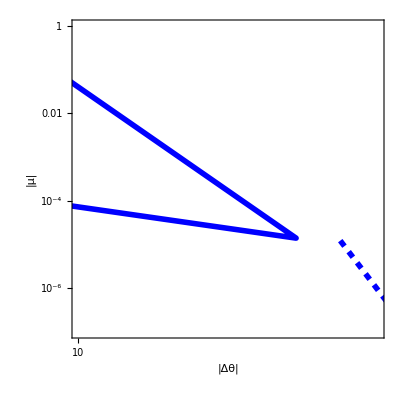

```mathematica
Show[ParametricPlot[{
{Log[10,Abs[(((θ/.tsc[[1]])-beta))/mas]/.beta->-b/.Δne->-Δnes[[3]]],
Log[10,Abs[μ/.tsc[[1]]]/.Δne->-Δnes[[3]]/.beta->-b]}},
{b,0.001*mas,10000000.*mas},PlotPoints->100,Frame->{True,True,False,False},Axes->False,
FrameTicks->{ticks,ticks,ticks,ticks},PlotRange->{{1.,4.},{-7.,0.}},FrameLabel->{"|Δθ|","|μ|"},PlotStyle->{Directive[Blue,Thickness[0.01]]},ImageSize->400,ImagePadding->{{60,60},{60,60}},AspectRatio->1],ParametricPlot[{
{Log[10,Abs[(((θ/.tinner[[1]])-betainner))/mas]/.Δne->-Δnes[[3]]],
Log[10,Abs[(muinner/.tinner[[1]])]/.Δne->-Δnes[[3]]]}},
{betainner,(t/2+s Δn Sqrt[2*r/t])/.Δne->-Δnes[[3]],100000.*mas},PlotPoints->100,Frame->{True,True,False,False},Axes->False,
FrameTicks->{ticks,ticks,ticks,ticks},PlotRange->All,FrameLabel->{"|Δθ|","|μ|"},PlotStyle->{Directive[Blue,Dashed,Thickness[0.01]]},ImageSize->400,ImagePadding->{{60,60},{60,60}},AspectRatio->1]
]
```

```mathematica
dthetamin=s*Abs[Δn]*Sqrt[2r/t]
```

6.77692×10^-11 Abs[Δne]

```mathematica
dthetamin/mas/.Δne->Δnes[[1]]
```

41.9352

```mathematica
Δnes[[3]]
```

300000.

```mathematica
c
```

2.99792×10^8

```mathematica
s
```

0.372581

```mathematica
Sqrt[2*c*0.995*^-3*s/(dpsr*(1-s))]/mas
```

28.0686